```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v4/Tpc

### Model

```mathematica
mub={0,100,200,300,400,500,550};
T=Table[i,{i,1,300}];
mfmub0=Transpose[{T,Transpose[Import["./mub0/BUFFER/MF.DAT"]][[1]]}];
mfmub100=Transpose[{T,Transpose[Import["./mub100/BUFFER/MF.DAT"]][[1]]}];
mfmub200=Transpose[{T,Transpose[Import["./mub200/BUFFER/MF.DAT"]][[1]]}];
mfmub300=Transpose[{T,Transpose[Import["./mub300/BUFFER/MF.DAT"]][[1]]}];
mfmub400=Transpose[{T,Transpose[Import["./mub400/BUFFER/MF.DAT"]][[1]]}];
mfmub500=Transpose[{T,Transpose[Import["./mub500/BUFFER/MF.DAT"]][[1]]}];
mfmub550=Transpose[{T,Transpose[Import["./mub550/BUFFER/MF.DAT"]][[1]]}];
```

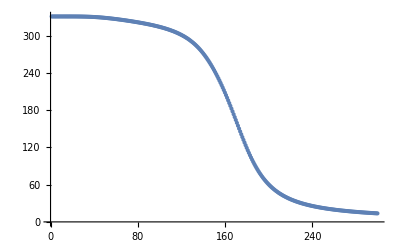

```mathematica
ListPlot[{mfmub0}]
```

```mathematica
dmfdTmub0=Table[-D[Interpolation[mfmub0][x],x][[0]][i],{i,1,300}];
dmfdTmub100=Table[-D[Interpolation[mfmub100][x],x][[0]][i],{i,1,300}];
dmfdTmub200=Table[-D[Interpolation[mfmub200][x],x][[0]][i],{i,1,300}];
dmfdTmub300=Table[-D[Interpolation[mfmub300][x],x][[0]][i],{i,1,300}];
dmfdTmub400=Table[-D[Interpolation[mfmub400][x],x][[0]][i],{i,1,300}];
dmfdTmub500=Table[-D[Interpolation[mfmub500][x],x][[0]][i],{i,1,300}];
dmfdTmub550=Table[-D[Interpolation[mfmub550][x],x][[0]][i],{i,1,300}];
```

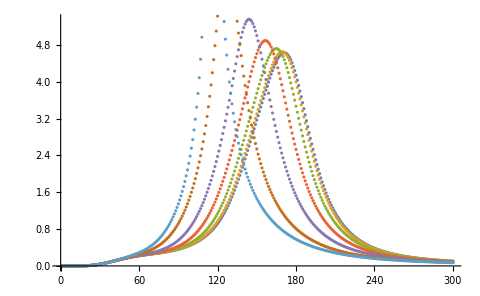

```mathematica
ListPlot[{dmfdTmub0,dmfdTmub100,dmfdTmub200,dmfdTmub300,dmfdTmub400,dmfdTmub500,dmfdTmub550}]
```

```mathematica
Export["./data/mfmub0.dat",Transpose[mfmub0][[2]]];
Export["./data/mfmub100.dat",Transpose[mfmub100][[2]]];
Export["./data/mfmub200.dat",Transpose[mfmub200][[2]]];
Export["./data/mfmub300.dat",Transpose[mfmub300][[2]]];
Export["./data/mfmub400.dat",Transpose[mfmub400][[2]]];
Export["./data/mfmub500.dat",Transpose[mfmub500][[2]]];
Export["./data/mfmub550.dat",Transpose[mfmub550][[2]]];
```

```mathematica
Export["./data/dmfdTmub0.dat",dmfdTmub0];
Export["./data/dmfdTmub100.dat",dmfdTmub100];
Export["./data/dmfdTmub200.dat",dmfdTmub200];
Export["./data/dmfdTmub300.dat",dmfdTmub300];
Export["./data/dmfdTmub400.dat",dmfdTmub400];
Export["./data/dmfdTmub500.dat",dmfdTmub500];
Export["./data/dmfdTmub550.dat",dmfdTmub550];
```

```mathematica
(*lmub0=Transpose[{T,Transpose[Import["./mub0/TemB1/BUFFER/l.DAT"]][[1]]}];
dldTmub0=Table[D[Interpolation[lmub0][x],x][[0]][i],{i,1,250}];*)
```

```mathematica
(*ListPlot[lmub0]*)
```

```mathematica
(*ListPlot[{dmfdTmub0,dldTmub0*550},PlotLegends->{"dmf/dT","dL/dT"},AxesLabel->{"T","dO/dT"}]*)
```

```mathematica
(*Export["dldTmub0.dat",dldTmub0];*)
```